# Comparing date addition and subtraction

Peter Cullen Burbery

I aim to compare date addition methods such as roll over, roll forward.

In 13.1 DatePlus and DateDifference were given a new method option for how computations should be made.

My birthday was at Cabell-Huntington hospital in Huntington West Virginia at 11:45 pm. I would like to think that it was 11:45:45pm to the second, so I'll go with that. The date was 18 February 2002 in the cold winter.

I will analyze dates with my birthday.

```mathematica
$birthday=DateObject["18 February 2002 11:45:45 pm",CalendarType->"Gregorian",DateFormat->"LocaleDateTimeFull",TimeZone->Entity["City",{"Huntington","WestVirginia","UnitedStates"}]]
```

Monday, February 18, 2002 at 10:45:45 PMEST

I'm not sure why the date doesn't display 11:45:45 but it probably has something to do with daylight savings time.

```mathematica
$18thbirthday=DatePlus[$birthday,{18,"Year"}]
```

Tuesday, February 18, 2020 at 10:45:45 PMEST

```mathematica
different18thbirthdays=AssociationMap[DatePlus[$birthday,{18,"Year"},Method->#]&,{"Continuous","RollForward","RollBackward","RollOver"}]
```

<|Continuous→Friday, February 14, 2020 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2020 at 10:45:45 PMEST,RollBackward→Tuesday, February 18, 2020 at 10:45:45 PMEST,RollOver→Tuesday, February 18, 2020 at 10:45:45 PMEST|>

I want to check if the values are all different.

```mathematica
DuplicateFreeQ[different18thbirthdays]
```

False

Let's delete the duplicates:

```mathematica
DeleteDuplicates[different18thbirthdays]
```

<|Continuous→Friday, February 14, 2020 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2020 at 10:45:45 PMEST|>

I think its interesting that if my 18th birthday was implemented with continuous time, I would have turned 18 on 14 February 2002.

Analyze the date difference:

```mathematica
DateDifference@@Values[DeleteDuplicates[different18thbirthdays]]
```

4 days

Make a table of my birthdays:

```mathematica
myBirthdays=AssociationMap[year↦AssociationMap[DatePlus[$birthday,{year,"Year"},Method->#]&,{"Continuous","RollForward","RollBackward","RollOver"}],Range[20]]
```

<|1→<|Continuous→Tuesday, February 18, 2003 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2003 at 10:45:45 PMEST,RollBackward→Tuesday, February 18, 2003 at 10:45:45 PMEST,RollOver→Tuesday, February 18, 2003 at 10:45:45 PMEST|>,2→<|Continuous→Wednesday, February 18, 2004 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2004 at 10:45:45 PMEST,RollBackward→Wednesday, February 18, 2004 at 10:45:45 PMEST,RollOver→Wednesday, February 18, 2004 at 10:45:45 PMEST|>,3→<|Continuous→Thursday, February 17, 2005 at 10:45:45 PMEST,RollForward→Friday, February 18, 2005 at 10:45:45 PMEST,RollBackward→Friday, February 18, 2005 at 10:45:45 PMEST,RollOver→Friday, February 18, 2005 at 10:45:45 PMEST|>,4→<|Continuous→Friday, February 17, 2006 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2006 at 10:45:45 PMEST,RollBackward→Saturday, February 18, 2006 at 10:45:45 PMEST,RollOver→Saturday, February 18, 2006 at 10:45:45 PMEST|>,5→<|Continuous→Saturday, February 17, 2007 at 10:45:45 PMEST,RollForward→Sunday, February 18, 2007 at 10:45:45 PMEST,RollBackward→Sunday, February 18, 2007 at 10:45:45 PMEST,RollOver→Sunday, February 18, 2007 at 10:45:45 PMEST|>,6→<|Continuous→Sunday, February 17, 2008 at 10:45:45 PMEST,RollForward→Monday, February 18, 2008 at 10:45:45 PMEST,RollBackward→Monday, February 18, 2008 at 10:45:45 PMEST,RollOver→Monday, February 18, 2008 at 10:45:45 PMEST|>,7→<|Continuous→Monday, February 16, 2009 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2009 at 10:45:45 PMEST,RollBackward→Wednesday, February 18, 2009 at 10:45:45 PMEST,RollOver→Wednesday, February 18, 2009 at 10:45:45 PMEST|>,8→<|Continuous→Tuesday, February 16, 2010 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2010 at 10:45:45 PMEST,RollBackward→Thursday, February 18, 2010 at 10:45:45 PMEST,RollOver→Thursday, February 18, 2010 at 10:45:45 PMEST|>,9→<|Continuous→Wednesday, February 16, 2011 at 10:45:45 PMEST,RollForward→Friday, February 18, 2011 at 10:45:45 PMEST,RollBackward→Friday, February 18, 2011 at 10:45:45 PMEST,RollOver→Friday, February 18, 2011 at 10:45:45 PMEST|>,10→<|Continuous→Thursday, February 16, 2012 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2012 at 10:45:45 PMEST,RollBackward→Saturday, February 18, 2012 at 10:45:45 PMEST,RollOver→Saturday, February 18, 2012 at 10:45:45 PMEST|>,11→<|Continuous→Friday, February 15, 2013 at 10:45:45 PMEST,RollForward→Monday, February 18, 2013 at 10:45:45 PMEST,RollBackward→Monday, February 18, 2013 at 10:45:45 PMEST,RollOver→Monday, February 18, 2013 at 10:45:45 PMEST|>,12→<|Continuous→Saturday, February 15, 2014 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2014 at 10:45:45 PMEST,RollBackward→Tuesday, February 18, 2014 at 10:45:45 PMEST,RollOver→Tuesday, February 18, 2014 at 10:45:45 PMEST|>,13→<|Continuous→Sunday, February 15, 2015 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2015 at 10:45:45 PMEST,RollBackward→Wednesday, February 18, 2015 at 10:45:45 PMEST,RollOver→Wednesday, February 18, 2015 at 10:45:45 PMEST|>,14→<|Continuous→Monday, February 15, 2016 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2016 at 10:45:45 PMEST,RollBackward→Thursday, February 18, 2016 at 10:45:45 PMEST,RollOver→Thursday, February 18, 2016 at 10:45:45 PMEST|>,15→<|Continuous→Tuesday, February 14, 2017 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2017 at 10:45:45 PMEST,RollBackward→Saturday, February 18, 2017 at 10:45:45 PMEST,RollOver→Saturday, February 18, 2017 at 10:45:45 PMEST|>,16→<|Continuous→Wednesday, February 14, 2018 at 10:45:45 PMEST,RollForward→Sunday, February 18, 2018 at 10:45:45 PMEST,RollBackward→Sunday, February 18, 2018 at 10:45:45 PMEST,RollOver→Sunday, February 18, 2018 at 10:45:45 PMEST|>,17→<|Continuous→Thursday, February 14, 2019 at 10:45:45 PMEST,RollForward→Monday, February 18, 2019 at 10:45:45 PMEST,RollBackward→Monday, February 18, 2019 at 10:45:45 PMEST,RollOver→Monday, February 18, 2019 at 10:45:45 PMEST|>,18→<|Continuous→Friday, February 14, 2020 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2020 at 10:45:45 PMEST,RollBackward→Tuesday, February 18, 2020 at 10:45:45 PMEST,RollOver→Tuesday, February 18, 2020 at 10:45:45 PMEST|>,19→<|Continuous→Saturday, February 13, 2021 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2021 at 10:45:45 PMEST,RollBackward→Thursday, February 18, 2021 at 10:45:45 PMEST,RollOver→Thursday, February 18, 2021 at 10:45:45 PMEST|>,20→<|Continuous→Sunday, February 13, 2022 at 10:45:45 PMEST,RollForward→Friday, February 18, 2022 at 10:45:45 PMEST,RollBackward→Friday, February 18, 2022 at 10:45:45 PMEST,RollOver→Friday, February 18, 2022 at 10:45:45 PMEST|>|>

```mathematica
Dataset[AssociationMap[year↦AssociationMap[DatePlus[$birthday,{year,"Year"},Method->#]&,{"Continuous","RollForward","RollBackward","RollOver"}],Range[20]]]
```

```mathematica
DeleteDuplicates/@myBirthdays
```

<|1→<|Continuous→Tuesday, February 18, 2003 at 10:45:45 PMEST|>,2→<|Continuous→Wednesday, February 18, 2004 at 10:45:45 PMEST|>,3→<|Continuous→Thursday, February 17, 2005 at 10:45:45 PMEST,RollForward→Friday, February 18, 2005 at 10:45:45 PMEST|>,4→<|Continuous→Friday, February 17, 2006 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2006 at 10:45:45 PMEST|>,5→<|Continuous→Saturday, February 17, 2007 at 10:45:45 PMEST,RollForward→Sunday, February 18, 2007 at 10:45:45 PMEST|>,6→<|Continuous→Sunday, February 17, 2008 at 10:45:45 PMEST,RollForward→Monday, February 18, 2008 at 10:45:45 PMEST|>,7→<|Continuous→Monday, February 16, 2009 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2009 at 10:45:45 PMEST|>,8→<|Continuous→Tuesday, February 16, 2010 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2010 at 10:45:45 PMEST|>,9→<|Continuous→Wednesday, February 16, 2011 at 10:45:45 PMEST,RollForward→Friday, February 18, 2011 at 10:45:45 PMEST|>,10→<|Continuous→Thursday, February 16, 2012 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2012 at 10:45:45 PMEST|>,11→<|Continuous→Friday, February 15, 2013 at 10:45:45 PMEST,RollForward→Monday, February 18, 2013 at 10:45:45 PMEST|>,12→<|Continuous→Saturday, February 15, 2014 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2014 at 10:45:45 PMEST|>,13→<|Continuous→Sunday, February 15, 2015 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2015 at 10:45:45 PMEST|>,14→<|Continuous→Monday, February 15, 2016 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2016 at 10:45:45 PMEST|>,15→<|Continuous→Tuesday, February 14, 2017 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2017 at 10:45:45 PMEST|>,16→<|Continuous→Wednesday, February 14, 2018 at 10:45:45 PMEST,RollForward→Sunday, February 18, 2018 at 10:45:45 PMEST|>,17→<|Continuous→Thursday, February 14, 2019 at 10:45:45 PMEST,RollForward→Monday, February 18, 2019 at 10:45:45 PMEST|>,18→<|Continuous→Friday, February 14, 2020 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2020 at 10:45:45 PMEST|>,19→<|Continuous→Saturday, February 13, 2021 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2021 at 10:45:45 PMEST|>,20→<|Continuous→Sunday, February 13, 2022 at 10:45:45 PMEST,RollForward→Friday, February 18, 2022 at 10:45:45 PMEST|>|>

Analyze the differences between continuous and roll forward. Which

First sort by length because the first years have only one element each, then by the difference between the dates:

```mathematica
ReverseSortBy[{Length,Now}][DeleteDuplicates/@myBirthdays]
```

<|20→<|Continuous→Sunday, February 13, 2022 at 10:45:45 PMEST,RollForward→Friday, February 18, 2022 at 10:45:45 PMEST|>,19→<|Continuous→Saturday, February 13, 2021 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2021 at 10:45:45 PMEST|>,18→<|Continuous→Friday, February 14, 2020 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2020 at 10:45:45 PMEST|>,17→<|Continuous→Thursday, February 14, 2019 at 10:45:45 PMEST,RollForward→Monday, February 18, 2019 at 10:45:45 PMEST|>,16→<|Continuous→Wednesday, February 14, 2018 at 10:45:45 PMEST,RollForward→Sunday, February 18, 2018 at 10:45:45 PMEST|>,15→<|Continuous→Tuesday, February 14, 2017 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2017 at 10:45:45 PMEST|>,14→<|Continuous→Monday, February 15, 2016 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2016 at 10:45:45 PMEST|>,13→<|Continuous→Sunday, February 15, 2015 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2015 at 10:45:45 PMEST|>,12→<|Continuous→Saturday, February 15, 2014 at 10:45:45 PMEST,RollForward→Tuesday, February 18, 2014 at 10:45:45 PMEST|>,11→<|Continuous→Friday, February 15, 2013 at 10:45:45 PMEST,RollForward→Monday, February 18, 2013 at 10:45:45 PMEST|>,10→<|Continuous→Thursday, February 16, 2012 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2012 at 10:45:45 PMEST|>,9→<|Continuous→Wednesday, February 16, 2011 at 10:45:45 PMEST,RollForward→Friday, February 18, 2011 at 10:45:45 PMEST|>,8→<|Continuous→Tuesday, February 16, 2010 at 10:45:45 PMEST,RollForward→Thursday, February 18, 2010 at 10:45:45 PMEST|>,7→<|Continuous→Monday, February 16, 2009 at 10:45:45 PMEST,RollForward→Wednesday, February 18, 2009 at 10:45:45 PMEST|>,6→<|Continuous→Sunday, February 17, 2008 at 10:45:45 PMEST,RollForward→Monday, February 18, 2008 at 10:45:45 PMEST|>,5→<|Continuous→Saturday, February 17, 2007 at 10:45:45 PMEST,RollForward→Sunday, February 18, 2007 at 10:45:45 PMEST|>,4→<|Continuous→Friday, February 17, 2006 at 10:45:45 PMEST,RollForward→Saturday, February 18, 2006 at 10:45:45 PMEST|>,3→<|Continuous→Thursday, February 17, 2005 at 10:45:45 PMEST,RollForward→Friday, February 18, 2005 at 10:45:45 PMEST|>,2→<|Continuous→Wednesday, February 18, 2004 at 10:45:45 PMEST|>,1→<|Continuous→Tuesday, February 18, 2003 at 10:45:45 PMEST|>|>

```mathematica
Differences@*Values@*DeleteDuplicates/@myBirthdays
```

<|1→{},2→{},3→{1 day},4→{1 day},5→{1 day},6→{1 day},7→{2 days},8→{2 days},9→{2 days},10→{2 days},11→{3 days},12→{3 days},13→{3 days},14→{3 days},15→{4 days},16→{4 days},17→{4 days},18→{4 days},19→{5 days},20→{5 days}|>

```mathematica
DeleteCases[Differences@*Values@*DeleteDuplicates/@myBirthdays,{}]
```

<|3→{1 day},4→{1 day},5→{1 day},6→{1 day},7→{2 days},8→{2 days},9→{2 days},10→{2 days},11→{3 days},12→{3 days},13→{3 days},14→{3 days},15→{4 days},16→{4 days},17→{4 days},18→{4 days},19→{5 days},20→{5 days}|>

Now I can map first over the association.

```mathematica
First/@DeleteCases[Differences@*Values@*DeleteDuplicates/@myBirthdays,{}]
```

<|3→1 day,4→1 day,5→1 day,6→1 day,7→2 days,8→2 days,9→2 days,10→2 days,11→3 days,12→3 days,13→3 days,14→3 days,15→4 days,16→4 days,17→4 days,18→4 days,19→5 days,20→5 days|>

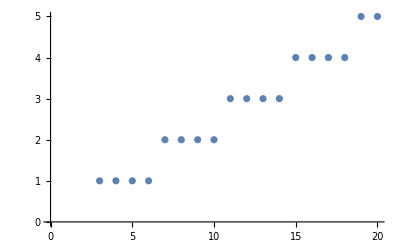

```mathematica
ListPlot[First/@DeleteCases[Differences@*Values@*DeleteDuplicates/@myBirthdays,{}]]
```

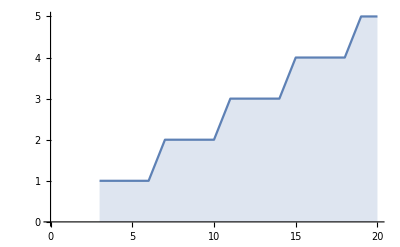

```mathematica
ListLinePlot[First/@DeleteCases[Differences@*Values@*DeleteDuplicates/@myBirthdays,{}],Filling->Bottom]
```

I think it looks like every four years a difference of one happens based on the ListPlot.

Make a function for my age:

```mathematica
Now-$birthday
```

7543.56 days

```mathematica
ageAssociation=AssociationMap[DateDifference[Now,$birthday,Method->#]&,{"Continuous","RollForward","RollBackward","RollOver"}]
```

<|Continuous→-7543.56 days,RollForward→-7543.56 days,RollBackward→-7543.56 days,RollOver→-7543.56 days|>

Delete duplicates.

```mathematica
DeleteDuplicates[ageAssociation]
```

<|Continuous→-7543.56 days,RollForward→-7543.56 days|>

It seems there is a difference in the methods, but its the computer's evaluation not the methods:

```mathematica
First@Differences@Values@DeleteDuplicates[ageAssociation]//UnitConvert
```

-1.57161×10^-7 s

```mathematica
UnitSimplify[First@Differences@Values@DeleteDuplicates[ageAssociation]//UnitConvert]
```

-0.157161 μs

```mathematica
age[]:=Now-$birthday
```

```mathematica
age[]
```

7543.56 days

```mathematica
UnitConvert[age[],MixedUnit[{"Megaseconds","Kiloseconds","Seconds"}]]
```

651 763

I want to compare some large times so I'm going to add the age of the Earth.

```mathematica
$earthsage=Entity["Planet","Earth"][EntityProperty["Planet","Age"]]
```

4.54×10^9 yr

The age of the Earth is not known to enough precision to be interesting.

```mathematica
UnitConvert[UnitConvert[$earthsage],MixedUnit[{"Petaseconds","Teraseconds","Gigaseconds","Megaseconds"}]]
```

143 173

```mathematica
earthsageplusmyage=$earthsage+age[]
```

1.6571×10^12 days

```mathematica
UnitConvert[earthsageplusmyage,MixedUnit[{"Petaseconds","Teraseconds","Gigaseconds","Megaseconds","Kiloseconds","Seconds"}]]
```

143 173

Time is bounded from below with the planck time:

```mathematica
UnitConvert[earthsageplusmyage,"PlanckTime"]
```

2.65566×10^60 t_P

See all the digits:

```mathematica
Floor[UnitConvert[earthsageplusmyage,"PlanckTime"]]
```

2655664647747805772063459302962182337410744394112918962044928 t_P

See my age in the planck time:

```mathematica
PersistResourceFunction["PlanckUnitConversion"]
```

Success[…]

```mathematica
Floor[PlanckUnitConversion[age[]]]
```

12089304753902233320678345086292749596864729216712704 t_P

Make a short quiz on which units are used to express the age of the Earth:

```mathematica
QuestionObject["which units should the age of the Earth be measured in? If the value of the Earth's age have a value greater than than 1 when measured in this unit then select the answer",AssessmentFunction[{"s"->True,"ks"->True,"Ms"->True,"Gs"->True,"Ts"->True,"Ps"->True,"Es"->False,"Zs"->False,"Ys"->False},<|"ElementwiseAssessment" -> True|>]]
```